```mathematica
(*Importing data from text file and sphere moving along linear path *)

linData= Import["C:\Users\manas\OneDrive - Northwestern University\Northwestern\Robotics\Mathematica - Sphere\linear_data.txt", "Data"];
time=linData[[All,1]];
x=linData[[All,2]];
y=linData[[All,3]];

Manipulate[Graphics3D[Sphere[{x[[t]],y[[t]],R},R], Axes->True, AxesLabel -> {"x","y", "z"}],{t, 1, Length[time],1}]
```

Part::partd: Part specification x⟦1⟧ is longer than depth of object.

Part::partd: Part specification y⟦1⟧ is longer than depth of object.

```mathematica
(*Sphere with x, y, z arrow*)

Graphics3D[{Purple, Opacity@.2,Sphere[{0,0,R},R], Thick,Blue, Arrow[{{0,0,R},{0,0,2R}}], Thick, Red, Arrow[{{0,0,R},{R,0,R}}], Thick, Green, Arrow[{{0,0,R},{0,R,R}}]}, Axes->True, AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
(*Sphere that rolls and has accurate axes*)
```

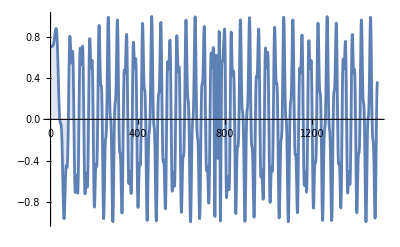

1.

```mathematica
R = 0.12;
r = 0.093;
phi=45Degree;

linData= Import["C:\Users\manas\OneDrive - Northwestern University\Northwestern\Robotics\Mathematica - Sphere\linear_data.txt", "Data"];
rotData = Import["C:\Users\manas\OneDrive - Northwestern University\Northwestern\Robotics\Mathematica - Sphere\angular_data.txt","Data"];
inpData = Import["C:\Users\manas\OneDrive - Northwestern University\Northwestern\Robotics\Mathematica - Sphere\input_data.txt", "Data"];

time=linData[[All,1]];
x=linData[[All,2]];
y=linData[[All,3]];
a = rotData[[All,2]];
b = rotData[[All,3]];
g = rotData[[All,4]];
theta = inpData[[All, 2]];

xAxes[t_]:=Flatten[EulerMatrix[{a[[t]],b[[t]],g[[t]]}].{{1},{0},{0}}]
yAxes[t_]:=Flatten[EulerMatrix[{a[[t]],b[[t]],g[[t]]}].{{0},{1},{0}}]
zAxes[t_]:=Flatten[EulerMatrix[{a[[t]],b[[t]],g[[t]]}].{{0},{0},{1}}]
pendulumDot[t_] := Flatten[EulerMatrix[{a[[t]],b[[t]],g[[t]]}].{{r*Sin[phi]*Cos[theta[[t]]]},{r*Sin[phi]*Sin[theta[[t]]]},{-r*Cos[phi]}}]
Manipulate[Graphics3D[{Purple, Opacity@0.2,Sphere[{x[[t]],y[[t]],R},R], 
					Thick, Red, Arrow[{{x[[t]],y[[t]],R},{x[[t]],y[[t]],R}+R*xAxes[t]}],
					Thick, Green, Arrow[{{x[[t]],y[[t]],R},{x[[t]],y[[t]],R}+R*yAxes[t]}],
					Thick, Blue, Arrow[{{x[[t]],y[[t]],R},{x[[t]],y[[t]],R}+R*zAxes[t]}],
					PointSize[Large],Point[{x[[t]],y[[t]],R}+pendulumDot[t]]},
					Axes->True, AxesLabel -> {"x","y", "z"}],{t, 1, Length[time],1}]
DiscretePlot[xAxes[t][[1]],{t,1500}]
Norm[xAxes[10]]
```